```mathematica
SetDirectory["/Users/mobileryan/Triplet-ESR"]
```

/Users/mobileryan/Triplet-ESR

```mathematica
Directory[]
```

C:\Users\goluc\Documents

```mathematica
SetDirectory["C:\\Users\\goluc\\Desktop\\nonLinearFit"]
```

C:\Users\goluc\Desktop\nonLinearFit

```mathematica
preData=Import["./test.dat","CSV" ];
{dimT, dump}=Dimensions[preData[[2;;-1]]]
BData=Drop[Drop[preData[[1]],1],-1];
dimB=Length[BData]
DataB[B_]:=Table[{preData[[i,1]],preData[[i,B+1]]},{i,2,dimT}]
DataT[t_]:=Table[{preData[[1,i]],preData[[t+1,i+1]]},{i,1,dimB}]
```

{1002,352}

350

```mathematica
tempData=preData[[2;;-1, 2;;-1]];
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
{Max[tempData], Min[tempData]}
```

-Graphics-

{Max[41.34,],Min[-34.17,]}

```mathematica
Manipulate[
Module[{dataT},
dataT=DataT[startT];
ListPlot[dataT,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startT]<>", Time = "<>ToString[preData[[startT+1,1]]]<>", Max = "<> ToString[Max[dataT[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataT[[1;;-1,2]]]]] 
],
{{startT,207},1,dimT,1}]
```

```mathematica
Manipulate[
Module[{dataB},
dataB=DataB[startB];
ListPlot[dataB,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startB]<>", B-field = "<>ToString[preData[[1,startB]]]<>", Max = "<> ToString[Max[dataB[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataB[[1;;-1,2]]]]]
] ,
{{startB,105},1,dimB,1}]
```

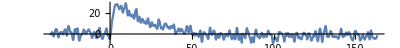

{B-Field,3.353,2.8,mean,0.765085,sd,2.9318}

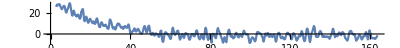

```mathematica
startB=139;
dataB=DataB[startB];
fitStartT=197;
ListPlot[dataB, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",BData[[startB]],dataB[[fitStartT,1]],"mean",noiseLevel=Mean[dataB[[1;;fitStartT-20,2]]], "sd",sd=StandardDeviation[dataB[[1;;fitStartT-20,2]]]}
g1=ListPlot[dataB[[fitStartT;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
f[t_,par_]:=Func[t,par[[1]],par[[2]]]+Func[t,par[[3]],par[[4]]]
F[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2,ⅇ^(-t/par[[4]]),(par[[3]] ⅇ^(-t/par[[4]]) t)/par[[4]]^2}
F2[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 200. | 4319.07 | 0.0463062 | 0.963078
Ta | 38.2491 | 52.5585 | 0.727743 | 0.466989
b | -166.699 | 4319.59 | -0.0385915 | 0.969226
Tb | 43.3092 | 68.3901 | 0.633266 | 0.526745, | DF | SS | MS
Model | 4 | 48394.6 | 12098.6
Error | 782 | 6159.93 | 7.87715
Uncorrected Total | 786 | 54554.5 | 
Corrected Total | 785 | 49204.8 | , | Estimate | Standard Error | Confidence Interval
a | 200. | 4319.07 | {-8278.35,8678.35}
Ta | 38.2491 | 52.5585 | {-64.9234,141.422}
b | -166.699 | 4319.59 | {-8646.06,8312.67}
Tb | 43.3092 | 68.3901 | {-90.9408,177.559}}

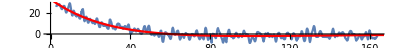

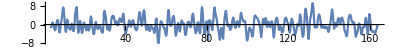

{mean,-0.027769,sd,2.7971,0.954054}

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-20]],{f[t,{a,Ta,b,Tb}], 200>a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb}, t];
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{dataB[[i,1]],dataB[[i,2]]-nlm[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff[[1;;-1,2]]], "sd",fitSigma=StandardDeviation[diff[[1;;-1,2]]], fitSigma/sd}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

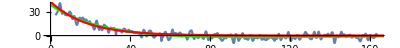

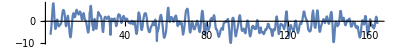

{mean,-1.00226,sd,3.05819,1.04221}

```mathematica
nlm2=NonlinearModelFit[dataB[[fitStartT;;-1]],{Func[t,a,Ta], 100>a>0, 0<Ta}, {a, Ta}, t];
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Green],
Plot[nlm2[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff2=Table[{dataB[[i,1]],dataB[[i,2]]-nlm2[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff2, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff2[[1;;-1,2]]], "sd",fitSigma2=StandardDeviation[diff2[[1;;-1,2]]], fitSigma2/sd}
```

## Manual Method

```mathematica
newPar[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, SSR, DF,dpar, GMat, fn, SSRn, SSRtmp, α},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[f[X[[i]], par],{i,Length[X]}];
Fa=Table[F[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
Print[Transpose[Fa].Fa//MatrixForm];
DF=Length[X]-Length[par];
SSR=(Y-fa).(Y-fa);
SSRtmp = SSR;
dpar=GMat.(Y-fa);
α=0.3;
Print["====================="];
Label[Loop];
par1=par+α  dpar;
fn =Table[f[X[[i]], par1],{i,Length[X]}];
SSRn=(Y - fn).(Y-fn);

If[SSRn < SSRtmp, 
SSRtmp = SSRn;
α = α * 1.05;
Goto[Loop];
];

Fn=Table[F[X[[i]], par1],{i,Length[X]}];
CoVar=SSRn/DF Inverse[Transpose[Fn].Fn];
(*Print[CoVar//MatrixForm];*)
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
Print[Transpose[Fa].(Y-fa)];
{par1,error, SSR, SSRn,dpar,DF, Transpose[Fa].(Y-fa), α}
]
```

```mathematica
temp=newPar[{55,28,-15,66},dataB[[fitStartT;;-20]]]
count =1;
While[Abs[temp[[3]]-temp[[4]]]>temp[[3]]*0.01 ||
Abs[temp[[5]][[1]]]>0.01 ||
Abs[temp[[5]][[2]]]>0.01 ||
Abs[temp[[5]][[3]]]>0.01 ||
Abs[temp[[5]][[4]]]>0.01,
Print[count];
temp=newPar[temp[[1]],dataB[[fitStartT;;-20]]];
count++;
]
temp
```

{{61.1673,30.5997,-23.3767,51.6096},{64.4435,9.70731,65.0374,35.4882},7810.8,8033.82,{20.5577,8.66568,-27.9225,-47.9682},782,{-303.545,-315.424,-431.409,29.4046},0.3}

$Aborted

{{37.6486,115.529,-7.99005,-34.0896},{34.9319,497.063,6.84749,6.12974},1.78218×10^10,6.06585×10^7,{132.158,35.2444,-131.651,-0.0406202},782,{-501356.,982329.,-1.34932×10^8,-2.20444×10^9},1.0667}

```mathematica
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 54.9534 | 14.2601 | 3.85365 | 0.000125915
Ta | 27.8581 | 4.00391 | 6.95771 | 7.31732×10^-12
b | -15.3043 | 14.7774 | -1.03566 | 0.300682
Tb | 65.5311 | 25.9996 | 2.52047 | 0.0119179, | DF | SS | MS
Model | 4 | 65153.6 | 16288.4
Error | 782 | 6789.3 | 8.68197
Uncorrected Total | 786 | 71942.9 | 
Corrected Total | 785 | 63656. | , | Estimate | Standard Error | Confidence Interval
a | 54.9534 | 14.2601 | {26.9608,82.9459}
Ta | 27.8581 | 4.00391 | {19.9984,35.7178}
b | -15.3043 | 14.7774 | {-44.3123,13.7037}
Tb | 65.5311 | 25.9996 | {14.4938,116.568}}

```mathematica
X=dataB[[fitStartT;;-20]][[1;;-1,1]];
Y=dataB[[fitStartT;;-20]][[1;;-1,2]];
SSRcoun= Table[{a, Ta, fn =Table[f[X[[i]], {52.3, 29.12, a, Ta}],{i,Length[X]}];
SSRn=(Y - fn).(Y-fn)},{a,-25,-5, 1}, {Ta, 20, 70,1}];
```

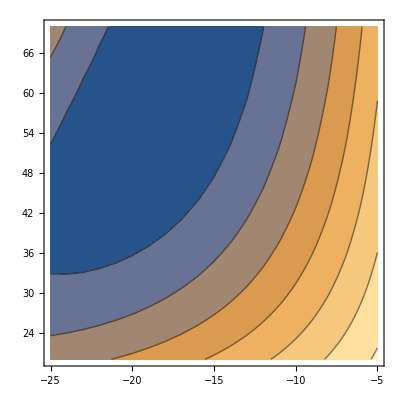

```mathematica
ListContourPlot[Flatten[SSRcoun,1]]
```

```mathematica
DF=803;α=0.95;
tStat=Table[temp[[1,i]]/temp[[2,i]],{i,1,4}]
pValue=Table[2(1-CDF[StudentTDistribution[DF],Abs[tStat[[i]]]]),{i,1,4}]
CF=Table[
temp[[1,i]]+
temp[[2,i]]{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]},{i,1,4}]
```

{1.74526,4.84665,-0.678331,2.36191}

{0.0813214,1.50736×10^-6,0.497757,0.018419}

{{-8.03612,136.909},{17.9915,42.4848},{-98.8684,48.0853},{9.37862,101.661}}

```mathematica
newPar2[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[Func[X[[i]], par[[1]],par[[2]]],{i,Length[X]}];
Fa=Table[F2[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp2=newPar2[{50,30},dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
```

{{42.0385,18.115},{1.32321,1.03401},47.0199,805}

{{43.21,18.0827},{0.909289,0.483381},10.8097,805}

{{43.1979,18.0916},{0.908267,0.468798},10.7557,805}

{{43.2012,18.0894},{0.907925,0.469012},10.7557,805}

{{43.2004,18.0899},{0.908009,0.468955},10.7557,805}

{{43.2006,18.0898},{0.907988,0.468969},10.7557,805}

{{43.2005,18.0898},{0.907994,0.468966},10.7557,805}

{{43.2005,18.0898},{0.907992,0.468966},10.7557,805}

```mathematica
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

```mathematica
DF2=805;α=0.95;
tStat2=Table[temp2[[1,i]]/temp2[[2,i]],{i,1,2}]
pValue2=Table[2(1-CDF[StudentTDistribution[DF2],Abs[tStat2[[i]]]]),{i,1,2}]
CF2=Table[
temp2[[1,i]]+
temp2[[2,i]]{InverseCDF[StudentTDistribution[DF2],(1-α)/2],InverseCDF[StudentTDistribution[DF2],(1+α)/2]},{i,1,2}]
```

{47.5777,38.5742}

{0.,0.}

{{41.4182,44.9828},{17.1693,19.0104}}